# Chapter 9

## Gauss Elimination

## Initialization

```mathematica
Needs["SchoolDisplay`"];
```

## Homework

### 9.5 System of Linear Equations

The first attempt at a solution to the system of equations is to plot the equations and determine their intersection. This is done by solving the systems of equations for one of the variables and plotting the line. Solving for x_2 and plotting shows that the graphical solution under magnification still does not yield a precise results. The solution lies within the intervals {x,y | x∈(0.99,10.01) y∈ (14.49,15.51)}.

The determinant of the coefficient matrix is nearly zero. This implies the two equations are nearly linearly-dependent (scalar multiples).

After modifing the value of a_(1,1) and solving the system of equations, the solution vector varied by 200% and 30% due to only a 4% modification of a single coefficient. These results again confirm that the system is ill-conditioned.

#### Code

```mathematica
$Line=0;
```

```mathematica
(* solve the equations and assign to functions *)
sol=Solve[{0.5 x1-x2 ==-9.5, 1.02 y1-2y2==-18.8},{#,#2}][[1]]&;
```

```mathematica
x2[x1_]=x2/.sol[x2,y2];
y2[y1_]=y2/.sol[x2,y2];
```

```mathematica
p=Plot[{x2@x,y2@x},{x,9.99,10.01},
FrameLabel->{"x","f(x)"},
PlotRange->{14.49,14.51},PlotTheme->"Detailed",PlotLabel->HoldForm@(x2==y2),ImageSize->Medium];
```

```mathematica
(* coefficient matrix and determinant *)
𝔸=({{0.5, -1.}, {1.02, -2.}});b⃗=({{-9.5}, {-18.8}});
Det@𝔸;
```

```mathematica
(* solving for unknowns *)
x⃗=LinearSolve[𝔸,b⃗]//Flatten
```

{10.,14.5}

```mathematica
(* altering the value of a[1,1] *)
```

```mathematica
𝔸δ=({{0.52, -1.}, {1.02, -2.}});
Det@𝔸δ;
```

```mathematica
OverVector[xδ]=LinearSolve[𝔸δ,b⃗]//Flatten;
```

```mathematica
{0.52/0.5,OverVector[xδ]/x⃗*100};
```

#### Output

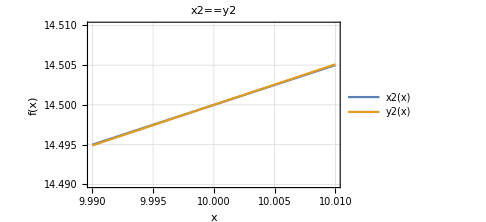
Plot
-Graphics-
Determinant
Det[𝔸]=0.02
System Condition
System is Ill-conditioned
Elimination of UNK
x⃗={10.,14.5}
Modified a[1,1]
OverVector[xδ]={-10.,4.3}
δa[1,1] ⇒ OverVector[xδ] 
{1.04,{-100.,29.6552}}Problem 9.5

```mathematica
DisplayColumn["Problem 9.5",{"Plot","Determinant","System Condition","Elimination of UNK","Modified a[1,1]","δa[1,1] ⇒ OverVector[xδ] "},
{p,
Row[{HoldForm@(Det@𝔸),"=",Det@𝔸}],
"System is Ill-conditioned",
Row[{HoldForm@x⃗,"=",Out@7}],
Row[{HoldForm@OverVector[xδ],"=",Out@11}],
Out@12
}
]
```

### 9.17 Stability of System

The Gaussian Elimination method has been altered so such that the determinant near zero now exists as a possible stopping condition. If the absolute value of the coefficient determinant is greater than the given tolerance, the execution will procede normally. If the absolute value of the coefficient determinant is less than the tolerance, an error message is returned “GaussPivotNew::tolerance” and execution halts.

```mathematica
𝔸=({{0.5, -1.}, {1.02, -2.}});b=({{-9.5}, {-18.8}});
```

```mathematica
GaussPivotNew::tolerance="Determinant is near zero. Singular array.";
GaussPivotNew[a_?MatrixQ,b_?MatrixQ,tolerance_:10.^(-6)]:=Block[{},
If[(Abs@#3) > tolerance,
Grid[{{"Det","x⃗"},{#3,LinearSolve[#,#2]}},Frame->All,Spacings->{1, 1}],
Message[GaussPivotNew::tolerance]
]&[#,#2,Det@#]&[a,b]
]
```

```mathematica
DisplayColumn["Problem 9.17",{"New Gauss Pivot"},{GaussPivotNew[𝔸,b,10.^-6]}]
```

New Gauss Pivot
Det | x⃗
0.02 | {{10.},{14.5}}Problem 9.17